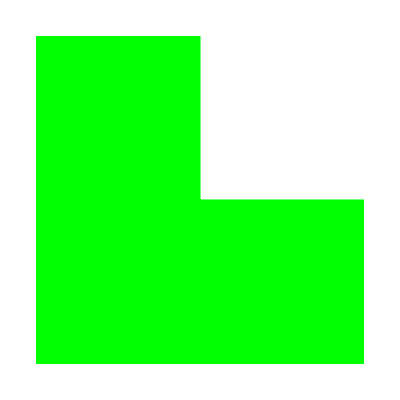

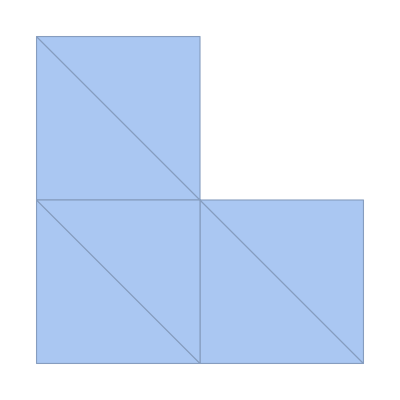

1

Part::partd: Part specification ()⟦1⟧ is longer than depth of object.

1

```mathematica
P={
{0,0},
{1,0},
{2,0},
{0,1},
{1,1},
{2,1},
{0,2},
{1,2}
};
T={
{1,2,4},
{2,5,4},
{2,3,5},
{3,6,5},
{4,5,7},
{5,8,7}
};
constructElements[nodes_,nodeIndexArr_]:=Polygon[Table[nodes⟦#⟦k⟧⟧,{k,1,Length[#]}]]&/@nodeIndexArr
triangleTable =constructElements[P,T];
Graphics[{EdgeForm[Directive[Dashed]],Green,triangleTable}]
meshTable=MeshRegion[P,Polygon/@T]

inRegion[regions_,coordinates_]:=Module[{ind=1,len=Length[regions];},
While[!(coordinates∈regions⟦ind⟧),
++ind;
If[ind>len,ind=0;Break[]]
];
ind
]
inRegion[triangleTable, {1,0}]
inRegion[meshTable, {1,0}]

hatFunctions[k_,nodes_?ListQ,nodeIndexArr_?ListQ,elements_?ListQ,coordinates_]:=Module[{elIndex=inRegion[elements,coordinates],dims=Length[nodes⟦1⟧]},
(*If it is not part of the region of elements, return 0*)
If[elIndex==0, Return[0]];
(*Take which index in vector equation must have non-zero in RHS*)
indexInPolygon=FirstPosition[nodeIndexArr⟦elIndex⟧,k];
If[MissingQ[indexInPolygon], Return[0]];
rhs=Table[0,dims];
rhs⟦indexInPolygon⟧=1;
(*Take which index in vector equation must have non-zero in RHS*)
]
nodeInterpolate[nodes_?ListQ,elements_?ListQ,f_,coordinates_]:=Module[{elIndex=inRegion[elements,coordinates],plane},
If[elIndex==0, Return[0]];

plane=Polygon[
Table[
Append[nodes⟦elIndex⟦k⟧⟧,f[nodes⟦elIndex⟦k⟧⟧]],
{k,1,Length[elements[elIndex]]}]
];
]
```

```mathematica
(*triangleTable = Function[element,
Triangle[Table[P⟦element⟦k⟧⟧,{k,1,Length[element]}]]
]/@T;
Position[triangleTable, RegionMember[_,{1,1}]]
Position[triangleTable, {0.5,0.5}∈_]*)
```